```mathematica
Exit
```

```mathematica
<<MaTeX`
```

```mathematica
LatexTicks[min_,max_,step_,mag_:1.3]:=Table[{x,MaTeX[ToString@NumberForm[x,{Infinity,1}],Magnification->mag]},{x,min,max,step}];
```

## Scalar Perturbation in PFDM

```mathematica
(*x^μ coordinates*)
```

```mathematica
x:={t,r,θ,ϕ};
(* Subscript[g, μν] metric coefficients *)
gdd := {{-f[r],0,0,0},{0,1/f[r],0,0},{0,0,r^2,0},{0,0,0,r^2 Sin[θ]^2}}

(*g^μν inverse metric coefficients*)
guu := Inverse[gdd];

gdd//MatrixForm;
guu //MatrixForm;

(*Multiplying the two metric*)
guu.gdd//MatrixForm;
Det[gdd]
```

-r^4 Sin[θ]^2

```mathematica
(*Klein-Gordon equation for scalar field*)
KG=Sum[1/(√(-Det[gdd]))D[√(-Det[gdd]) guu[[μ,ν]] D[Φ[t,r,θ,ϕ],x[[ν]]],x[[μ]]],{μ,1,4},{ν,1,4}] + m^2 Φ[t,r,θ,ϕ]//PowerExpand
```

m^2 Φ[t,r,θ,ϕ]+(Csc[θ]^2 Φ^(0,0,0,2)[t,r,θ,ϕ])/r^2+(Csc[θ] (Cos[θ] Φ^(0,0,1,0)[t,r,θ,ϕ]+Sin[θ] Φ^(0,0,2,0)[t,r,θ,ϕ]))/r^2+1/r^2 Csc[θ] (2 r f[r] Sin[θ] Φ^(0,1,0,0)[t,r,θ,ϕ]+r^2 Sin[θ] f'[r] Φ^(0,1,0,0)[t,r,θ,ϕ]+r^2 f[r] Sin[θ] Φ^(0,2,0,0)[t,r,θ,ϕ])-(Φ^(2,0,0,0)[t,r,θ,ϕ])/f[r]

```mathematica
Clear[R]
```

```mathematica
Φ[t_,r_,θ_,ϕ_]:=Exp[-I ω t] R[r]/r Y[θ,ϕ];
KG1 = Collect[KG r^3/(R[r]Y[θ,ϕ])Exp[I ω t],{Y[θ,ϕ],R[r]},Simplify]//Simplify
```

r (m^2 r+(r ω^2)/f[r]-f'[r])+(r^2 (f'[r] R'[r]+f[r] R''[r]))/R[r]+(Csc[θ]^2 Y^(0,2)[θ,ϕ]+Cot[θ] Y^(1,0)[θ,ϕ]+Y^(2,0)[θ,ϕ])/Y[θ,ϕ]

```mathematica
KG2 = KG1/.{(Csc[θ]^2 Derivative[0,2][Y][θ,ϕ]+Cot[θ] Derivative[1,0][Y][θ,ϕ]+Derivative[2,0][Y][θ,ϕ])/Y[θ,ϕ]->-L (L+1) }
```

-L (1+L)+r (m^2 r+(r ω^2)/f[r]-f'[r])+(r^2 (f'[r] R'[r]+f[r] R''[r]))/R[r]

```mathematica
Clear[R]
Collect[KG2 f[r]/r^2,{R''[r],R'[r],R[r]},Simplify]
```

ω^2-(f[r] (L+L^2-m^2 r^2+r f'[r]))/r^2+(f[r] f'[r] R'[r])/R[r]+(f[r]^2 R''[r])/R[r]

```mathematica
Clear[k,λ]
```

```mathematica
m=0.1
```

0.1

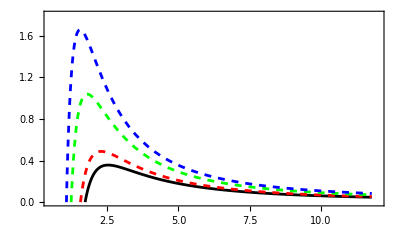

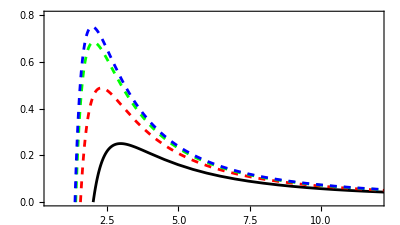

/Users/bakhodir/Theoretical_Physics/4thProjectQNM/v2.pdf

```mathematica
f[r_,k_,λ_]=1/(1-k)-2/r+λ/r Log[r/λ];
Veff[r_,L_,k_,λ_,m_]=(f[r,k,λ](L+L^2+m^2 r^2+r D[f[r,k,λ],r]))/r^2;
v1=Plot[{Veff[r,2,0.,0.1,0.1],Veff[r,2,0.1,0.1,0.1],Veff[r,2,0.3,0.1,0.1],Veff[r,2,0.4,0.1,0.1]},{r,.5,11.8},PlotRange->{{0.5,12},{0,1.8}},PlotStyle->{Black,{Red,Dashed},{Green,Dashed},{Blue,Dashed}},PlotLegends->Placed[{MaTeX["k=0",Magnification->1.3],MaTeX["k=0.1",Magnification->1.3],MaTeX["k=0.3",Magnification->1.3],MaTeX["k=0.4",Magnification->1.3]},{Scaled[{0.75,0.6}],{0.5,0.5}}],Frame->True,FrameLabel->{MaTeX["r/M",Magnification->1.3],MaTeX["V_{eff}",Magnification->1.3],MaTeX["\lambda/M=0.1,\quad \ell=2",Magnification->1.4]},LabelStyle->{FontFamily->"Times",Black,FontSize->14},AspectRatio->9/16]
Export["/Users/bakhodir/Theoretical_Physics/4thProjectQNM/v1.pdf",v1,"PDF"];
v2=Plot[{Veff[r,2,0.,0.0000001,0.1],Veff[r,2,0.1,0.1,0.1],Veff[r,2,0.1,0.3,0.1],Veff[r,2,0.1,0.4,0.1]},{r,.5,25},PlotRange->{{0.5,12},{0,0.8}},PlotStyle->{Black,{Red,Dashed},{Green,Dashed},{Blue,Dashed}},PlotLegends->Placed[{MaTeX["\lambda/M \\to 0",Magnification->1.3],MaTeX["\lambda/M=0.1",Magnification->1.3],MaTeX["\lambda/M=0.3",Magnification->1.3],MaTeX["\lambda/M=0.4",Magnification->1.3]},{Scaled[{0.7,0.6}],{0.5,0.5}}],Frame->True,FrameLabel->{MaTeX["r/M",Magnification->1.3],MaTeX["V_{eff}",Magnification->1.3],MaTeX["k=0.1,\quad \ell=2",Magnification->1.3]},LabelStyle->{FontFamily->"Times",Black,FontSize->14},AspectRatio->9/16]
Export["/Users/bakhodir/Theoretical_Physics/4thProjectQNM/v2.pdf",v2,"PDF"]
```

```mathematica
x[ra_,k_,λ_] :=NIntegrate[1/f[r,k,λ],{r,1.5,ra}]
```

```mathematica
FindRoot[]
```

```mathematica
Limit[(f[r,k,λ](L+L^2+m^2 r^2+r D[f[r,k,λ],r]))/r^2,r->Infinity]    (*When spatial infinity radiuses Veff depends on mass of scalar field*)
```

-0.01/(-1.+k)

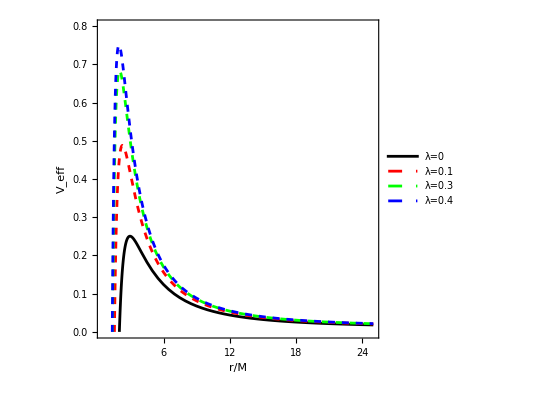

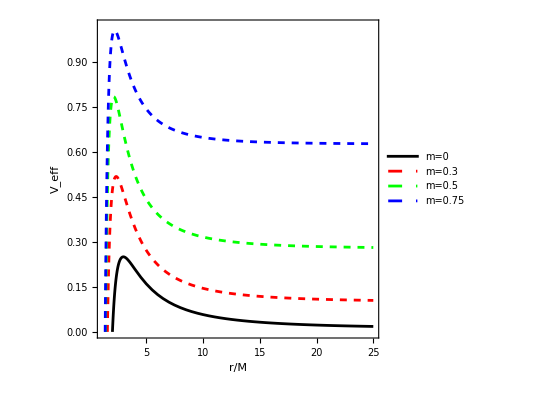

```mathematica
Plot[{Veff[r,2,0.,0.0000001,0.1],Veff[r,2,0.1,0.1,0.1],Veff[r,2,0.1,0.3,0.1],Veff[r,2,0.1,0.4,0.1]},{r,.5,25},PlotRange->{{0.5,25},{0,0.8}},PlotStyle->{Black,{Red,Dashed},{Green,Dashed},{Blue,Dashed}},PlotLegends->Placed[{"λ=0","λ=0.1","λ=0.3","λ=0.4"},{Scaled[{0.8,0.6}],{0.5,0.5}}],Frame->True,FrameLabel->{"r/M","V_eff","k=0.1, l=2"},LabelStyle->{FontFamily->"Times",Italic,Black,Bold,FontSize->13},AspectRatio->1]



Plot[{Veff[r,2,0.,0.0000001,0.1],Veff[r,2,0.1,0.1,0.3],Veff[r,2,0.1,0.3,.5],Veff[r,2,0.1,0.4,.75]},{r,.5,25},PlotRange->{{1.15,25},{0,1.02}},PlotStyle->{Black,{Red,Dashed},{Green,Dashed},{Blue,Dashed}},PlotLegends->Placed[{"m=0","m=0.3","m=0.5","m=0.75"},{Scaled[{0.8,0.6}],{0.5,0.5}}],Frame->True,FrameLabel->{"r/M","V_eff","k=0.1, l=2"},LabelStyle->{FontFamily->"Times",Italic,Black,Bold,FontSize->13},AspectRatio->1]
```

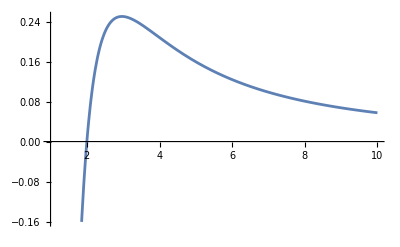

```mathematica
Plot[Veff[r,2,0.,0.0000001,0.1],{r,1,10}]
```

```mathematica
1
```

## Bh noBh reg

```mathematica
Clear[kk,λ]
```

```mathematica
f[r_,k_,λ_]=1/(1-k)-2/r+λ/r Log[r/λ];
```

```mathematica
D[f[r,k,λ],r]
```

2/r^2+λ/r^2-(λ Log[r/λ])/r^2

```mathematica
Filling[y==1]
```

Filling[y==1]

```mathematica
ContourPlot[2/r^2+λ/r^2-(λ Log[r/λ])/r^2==1/(1-k)-2/r+λ/r Log[r/λ],{k,0,0.3},{λ,10^-6,0.3},ContourShading]
```

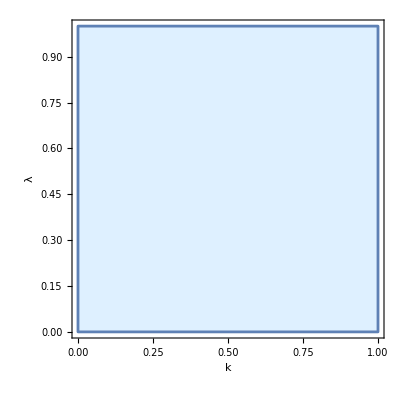

```mathematica
RegionPlot[0<=k<1&&0<λ<=1,{k,0,1},{λ,0,1},PlotStyle->LightBlue,Frame->True,Axes->False,FrameLabel->{Style["k",18],Style["λ",18]}]
```

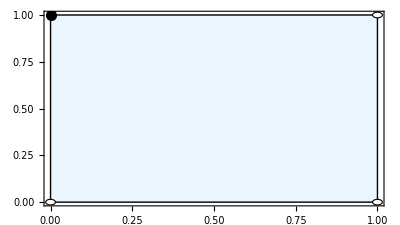

/Users/bakhodir/Theoretical Astrophysics/4thProjectQNM/bhregion.pdf

```mathematica
bhregion=Show[RegionPlot[0<=k<1&&0<λ<=1,{k,0,1},{λ,0,1},PlotStyle->Lighter[LightBlue],BoundaryStyle->Directive[Black,Thick],Frame->True,Axes->False,FrameLabel->{Style[MaTeX["k",Magnification->1.3],18],Style[MaTeX["\lambda",Magnification->1.3],18]}],Graphics[{White,EdgeForm[Black],Disk[{1,1},0.015],(*open circle at k=1*)Disk[{1,0},0.015],(*open circle*)Disk[{0,0},0.015],(*open circle*)Black,PointSize[0.02],Point[{0,1}]                 (*closed point*)}],FrameTicksStyle->Directive[FontSize->14,FontFamily->"Times",Black],AspectRatio->9/16]

Export["/Users/bakhodir/Theoretical Astrophysics/4thProjectQNM/bhregion.pdf",bhregion,"PDF"]
```

```mathematica
Solve[2+λ-λ Log[r/λ]==0,r]
```

{{r→ConditionalExpression[ⅇ^((2+λ)/λ) λ, -π<Im[(2+λ)/λ]≤π]}}

```mathematica
1/(1-k)-2/r+λ/r Log[r/λ]/.r->ⅇ^((2+λ)/λ) λ//FullSimplify
```

1/(1-k)+(ⅇ^(-1-2/λ) (-2+λ Log[ⅇ^((2+λ)/λ)]))/λ

```mathematica
Solve[1/(1-k)-(2 ⅇ^(-(2+λ)/λ))/λ+ⅇ^(-(2+λ)/λ) Log[ⅇ^((2+λ)/λ)]==0,k]
```

{{k→(-2+ⅇ^(1+2/λ) λ+λ Log[ⅇ^((2+λ)/λ)])/(-2+λ Log[ⅇ^((2+λ)/λ)])}}

```mathematica
Integrate[(x/r Log[r/x])^-1,r]
```

x ExpIntegralEi[2 Log[r/x]]

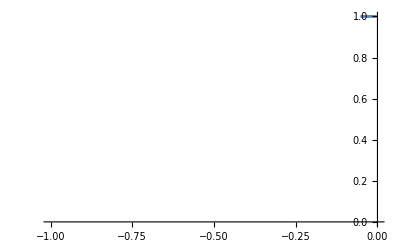

```mathematica
Plot[(-2+ⅇ^(1+2/λ) λ+λ Log[ⅇ^((2+λ)/λ)])/(-2+λ Log[ⅇ^((2+λ)/λ)]),{λ,-1,0},PlotRange->{0,1}]
```

```mathematica
ContourPlot[1/(1-k)-(2 ⅇ^(-(2+λ)/λ))/λ+ⅇ^(-(2+λ)/λ) Log[ⅇ^((2+λ)/λ)]==0,{λ,10^-2,0.4},{k,0,0.4}]
```

-Graphics-

```mathematica
Exit
```

```mathematica
rh[k_,λ_]:= r/.FindRoot[1/(1-k)-2/r+λ/r Log[r/λ]==0,{r,1.5}]
```

```mathematica
rh[0.,10]
```

57.4411

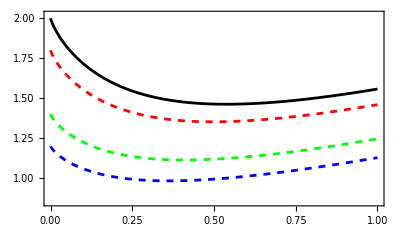

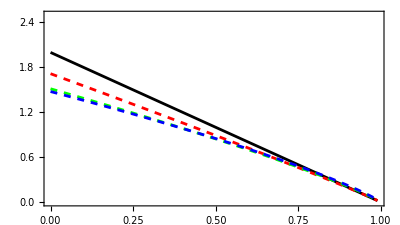

/Users/bakhodir/Theoretical_Physics/4thProjectQNM/h1.pdf

/Users/bakhodir/Theoretical_Physics/4thProjectQNM/h2.pdf

```mathematica
h1=Plot[{rh[0.,λ],rh[0.1,λ],rh[0.3,λ],rh[0.4,λ]},{λ,10^-6,1},Frame->True,FrameLabel->{MaTeX["\lambda/M",Magnification->1.3],MaTeX["r_h/M",Magnification->1.3]},PlotLegends->Placed[LineLegend[{MaTeX["k=0",Magnification->1.3],MaTeX["k=0.1",Magnification->1.3],MaTeX["k=0.3",Magnification->1.3],MaTeX["k=0.4",Magnification->1.3]},LegendLayout->{"Row",2}],{Scaled[{0.6,0.8}],{0.5,0.5}}],PlotStyle->{Black,{Red,Dashed},{Green,Dashed},{Blue,Dashed}},LabelStyle->{FontFamily->"Times",Black,FontSize->14},AspectRatio->9/16,PlotRange->{{10^-6,1},{0.85,2.02}}]

h2=Plot[{rh[k,10^-6],rh[k,0.1],rh[k,0.3],rh[k,0.4]},{k,0,0.99},Frame->True,FrameLabel->{MaTeX["k",Magnification->1.3],MaTeX["r_h/M",Magnification->1.3]},PlotLegends->Placed[LineLegend[{MaTeX["\lambda/M \\to 0",Magnification->1.3],MaTeX["\lambda/M=0.1",Magnification->1.3],MaTeX["\lambda/M=0.3",Magnification->1.3],MaTeX["\lambda/M=0.4",Magnification->1.3]},LegendLayout->{"Row",2}],{Scaled[{0.565,0.78}],{0.5,0.45}}],PlotStyle->{Black,{Red,Dashed},{Green,Dashed},{Blue,Dashed}},LabelStyle->{FontFamily->"Times",Black,FontSize->14},AspectRatio->9/16,PlotRange->{{0,.99},{0,2.5}}]
Export["/Users/bakhodir/Theoretical_Physics/4thProjectQNM/h1.pdf",h1,"PDF"]
Export["/Users/bakhodir/Theoretical_Physics/4thProjectQNM/h2.pdf",h2,"PDF"]
```

```mathematica
D[(f[r,k,λ](L+L^2+m^2 r^2+r D[f[r,k,λ],r]))/r^2,r]//Simplify
```

1/((-1.+k) r^5)(-16.+6. r-6. L r-6. L^2 r+2. L r^2+2. L^2 r^2-0.02 r^3-12. λ+4. r λ-1. L r λ-1. L^2 r λ-0.01 r^3 λ-1. λ^2+k (16.+r^3 (0.02+0.01 λ)+12. λ+1. λ^2+L r (6.+1. λ)+L^2 r (6.+1. λ))+λ (16.+(-3.+3. L+3. L^2) r+0.01 r^3+k (-16.-3. L r-3. L^2 r-0.01 r^3-6. λ)+6. λ) Log[r/λ]+(-4.+4. k) λ^2 Log[r/λ]^2)

```mathematica
rp[k_,λ_,L_,m_]:=r/.FindRoot[-1/((-1+k) r^5)(16-6 r+6 L r+6 L^2 r-2 L r^2-2 L^2 r^2+2 m^2 r^3+12 λ-4 r λ+L r λ+L^2 r λ+m^2 r^3 λ+λ^2-k (16+12 λ+λ^2+m^2 r^3 (2+λ)+L r (6+λ)+L^2 r (6+λ))-λ (16+3 (-1+L+L^2) r+m^2 r^3+6 λ-k (16+3 L r+3 L^2 r+m^2 r^3+6 λ)) Log[r/λ]-4 (-1+k) λ^2 Log[r/λ]^2)==0,{r,2}]
```

```mathematica
rp[0.,0.000001,2,0.1]
```

2.9644

```mathematica
Vp[k_,λ_,L_,m_]:=D[Veff[r,L,k,λ,m],r,r]/.r->rp[k,λ,L,m]
```

```mathematica
Vp[0.,0.000001,2,0.1]
```

-0.177435

```mathematica
dr[k_,λ_,L_] :=rp[k,λ,L]-rh[k,λ]
```

```mathematica
dr[0.4,0.1,2]
```

0.479985

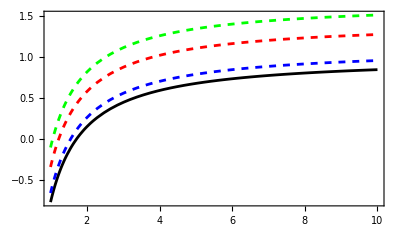

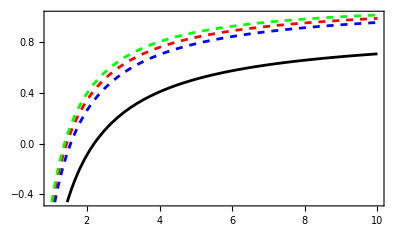

/Users/bakhodir/Theoretical_Physics/4thProjectQNM/mf1.pdf

/Users/bakhodir/Theoretical_Physics/4thProjectQNM/mf2.pdf

```mathematica
mf1=Plot[{f[r,0.,0.1],f[r,0.1,0.1],f[r,0.3,0.1],f[r,0.4,.1]},{r,1,10},Frame->True,FrameLabel->{MaTeX["r/M",Magnification->1.3],MaTeX["f(r)",Magnification->1.3],MaTeX["\lambda/M=0.1",Magnification->1.3]},PlotLegends->Placed[LineLegend[{MaTeX["k=0",Magnification->1.3],MaTeX["k=0.1",Magnification->1.3],MaTeX["k=0.3",Magnification->1.3],MaTeX["k=0.4",Magnification->1.3]},LegendLayout->{"Row",2}],{Scaled[{0.6,0.18}],{0.5,0.5}}],PlotStyle->{Black,{Blue ,Dashed},{Red,Dashed},{Green,Dashed}},LabelStyle->{FontFamily->"Times",Black,FontSize->14},AspectRatio->9/16]


mf2=Plot[{f[r,-0.1,10^-6],f[r,0.1,0.1],f[r,0.1,0.2],f[r,0.1,0.3]},{r,1,10},Frame->True,FrameLabel->{MaTeX["r/M",Magnification->1.3],MaTeX["f(r)",Magnification->1.3],MaTeX["k=0.1",Magnification->1.3]},PlotLegends->Placed[{MaTeX["\lambda/M \\to 0",Magnification->1.3],MaTeX["\lambda/M=0.1",Magnification->1.3],MaTeX["\lambda/M=0.3",Magnification->1.3],MaTeX["\lambda/M=0.4",Magnification->1.3]},{Scaled[{0.75,0.35}],{0.5,0.5}}],PlotStyle->{Black,{Blue,Dashed},{Red,Dashed},{Green,Dashed}},LabelStyle->{FontFamily->"Times",Black,FontSize->14},AspectRatio->9/16]
Export["/Users/bakhodir/Theoretical_Physics/4thProjectQNM/mf1.pdf",mf1,"PDF"]
Export["/Users/bakhodir/Theoretical_Physics/4thProjectQNM/mf2.pdf",mf2,"PDF"]
```

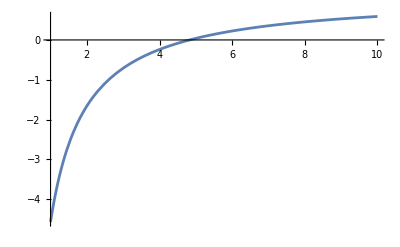

```mathematica
Plot[1/(1-0.1)-(2 *3)/r+0.2/r Log[r/0.2],{r,1,10}]
```

```mathematica
Limit[f[r,k,λ],λ->Infinity]
```

(-∞)/r

```mathematica
Limit[x Log[1/x],x->0]
```

0

## Frequency expression

```mathematica
k=0.2;
λ=0.1;
l=2;
```

```mathematica
(*k=0.2, λ = 0.1 max point*)
```

```mathematica
ω[k_,l_,λ_,n_,m_]:= (l(l+2)f[rp[k,λ,l,m],k,λ])/(rp[k,λ,l,m]^2 √(2 Vp[k,λ,l,m])) - ⅈ (n + 1/2)f[rp[k,λ,l,m],k,λ] √(2Vp[k,λ,l,m])
```

```mathematica
ω[0,2,0.1,0,0.2]
```

0.139711-0.51735 ⅈ

```mathematica
Clear[rp,k,l,λ]
```

```mathematica
ωRe[k_,λ_,l_,m_]:=(√(l(l+1) f[rp[k,λ,l,m],k,λ]))/rp[k,λ,l,m]
ωIm[k_,λ_,l_,n_,m_]:=-(n+1/2) 1/(√2)√Abs[Vp[k,λ,l,m]/ωRe[k,λ,l,m]];
```

```mathematica
ωRe[0.,0.1,2,0.2]
```

0.562328

```mathematica
rp[0,10^-6,2,0]
```

2.95169

```mathematica
ωIm[-0.2,0.2,2,0,0.]   (*1st ly should check for Schw*)
```

-(√Abs[(rp[-0.2,0.2,2,0.] Vp[-0.2,0.2,2,0.])/(√f[rp[-0.2,0.2,2,0.],-0.2,0.2])])/(2 2^(3/4) 3^(1/4))

```mathematica
V[r_]=(f[r,k,λ](L+L^2+m^2 r^2+r D[f[r,k,λ],r]))/r^2;
r/.Solve[V'[r]==0,r]
```

Solve::inex: Solve was unable to solve the system with inexact coefficients or the system obtained by direct rationalization of inexact numbers present in the system. Since many of the methods used by Solve require exact input, providing Solve with an exact version of the system may help.

ReplaceAll::reps: {Solve[((1.25-2 Power[«2»]+0.1 Power[«2»] Log[«1»]) (2.1 Power[«2»]+0.02 r-0.1 Power[«2»] Log[«1»]+r Plus[«2»]))/r^2+((2.1 Power[«2»]-0.1 Power[«1»] Log[«1»]) «1»)/r^2-(2 («1») (L+L^2+0.01 Power[«2»]+r Plus[«2»]))/r^3==0,r]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

r/.Solve[((1.25-2/r+(0.1 Log[10. r])/r) (2.1/r^2+0.02 r-(0.1 Log[10. r])/r^2+r (-4.3/r^3+(0.2 Log[10. r])/r^3)))/r^2+((2.1/r^2-(0.1 Log[10. r])/r^2) (L+L^2+0.01 r^2+r (2.1/r^2-(0.1 Log[10. r])/r^2)))/r^2-(2 (1.25-2/r+(0.1 Log[10. r])/r) (L+L^2+0.01 r^2+r (2.1/r^2-(0.1 Log[10. r])/r^2)))/r^3==0,r]

```mathematica
Clear[ω,V,U,n]
```

```mathematica
Vp3[k_,λ_,l_,m_]:=D[Veff[r,l,k,λ,m],{r,3}]/.r->rp[k,λ,l,m]

Vp4[k_,λ_,l_,m_]:=D[Veff[r,l,k,λ,m],{r,4}]/.r->rp[k,λ,l,m]
```

```mathematica
Solve[I((ω^2-V)/(√(-2 U)))- 1/(2 U)(1/8 V4/U (1/4 + (n+1/2)^2)-1/288 (V3/U)^2(7+60 (n+1/2)^2))== n+1/2,ω]//Simplify  (*U = f^2 V''(rp)*)
```

{{ω→((-1/2)^(1/4) U^(3/2) √((144 (1+2 n) U^3-144 ⅈ √2 (-U)^(5/2) V-(11+30 n+30 n^2) V3^2+9 (1+2 n+2 n^2) U V4)/U^3))/(12 (-U)^(5/4))},{ω→((-1/2)^(1/4) √U √((144 (1+2 n) U^3-144 ⅈ √2 (-U)^(5/2) V-(11+30 n+30 n^2) V3^2+9 (1+2 n+2 n^2) U V4)/U^3))/(12 (-U)^(1/4))}}

```mathematica
Clear[ω1]
```

```mathematica
ω1[k_,λ_,l_,n_,m_]:=1/((-f[rp[k,λ,l,m],k,λ]^2 (Vp[k,λ,l,m]))^(5/4))(-1/2)^(1/4) (f[rp[k,λ,l,m],k,λ]^2 (Vp[k,λ,l,m]))^(3/2) √(1+2 n+(ⅈ √2 Veff[rp[k,λ,l,m],l,k,λ,m])/(√(-f[rp[k,λ,l,m],k,λ]^2 (Vp[k,λ,l,m]))))
```

```mathematica
ω1[0.1,0.1,2,0,0.2]
```

0.72053-0.141347 ⅈ

```mathematica
ω1[0.2,0.1,2,0,0.2]
```

0.859602-0.178667 ⅈ

```mathematica
ω1[0.1,0.4,2,0,0.2]
```

0.769731-0.159701 ⅈ

```mathematica
ω1[0,10^-6,3,0,0]
```

0.694082-0.0960441 ⅈ

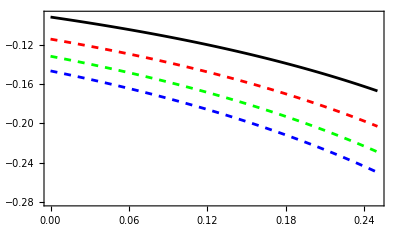

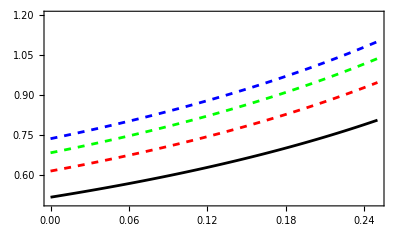

/Users/bakhodir/Theoretical Astrophysics/4thProjectQNM/freqIm1.pdf

/Users/bakhodir/Theoretical Astrophysics/4thProjectQNM/freqRe1.pdf

```mathematica
freqIm1=Plot[{ω1[k,10^-6,2,0,0.2]//Im,ω1[k,0.1,2,0,0.2]//Im,ω1[k,0.2,2,0,0.2]//Im,ω1[k,0.3,2,0,0.2]//Im},{k,0,0.25},Frame->True,FrameLabel->{MaTeX["k",Magnification->1.3],MaTeX["Im{(\omega)}",Magnification->1.3],MaTeX["\ell=2, m=0.2, n=0",Magnification->1.3]},PlotLegends->Placed[LineLegend[{MaTeX["\lambda \\to 0",Magnification->1.3],MaTeX["\lambda=0.1",Magnification->1.3],MaTeX["\lambda=0.2",Magnification->1.3],MaTeX["\lambda=0.3",Magnification->1.3]},LegendLayout->{"Row",2}],{Scaled[{0.35,0.2}],{0.5,0.5}}],PlotStyle->{Black,{Red,Dashed},{Green,Dashed},{Blue,Dashed}},LabelStyle->{FontFamily->"Times",Black,FontSize->14},AspectRatio->9/16,PlotRange->{{0,0.25},{-0.28,-0.09}}]


freqRe1=Plot[{ω1[k,10^-6,2,0,0.2]//Re,ω1[k,0.1,2,0,0.2]//Re,ω1[k,0.2,2,0,0.2]//Re,ω1[k,0.3,2,0,0.2]//Re},{k,0,0.25},Frame->True,FrameLabel->{MaTeX["k",Magnification->1.3],MaTeX["Re{(\omega)}",Magnification->1.3],MaTeX["\ell=2, m=0.2, n=0",Magnification->1.3]},PlotLegends->Placed[LineLegend[{MaTeX["\lambda \\to 0",Magnification->1.3],MaTeX["\lambda=0.1",Magnification->1.3],MaTeX["\lambda=0.2",Magnification->1.3],MaTeX["\lambda=0.3",Magnification->1.3]},LegendLayout->{"Row",2}],{Scaled[{0.35,0.8}],{0.5,0.5}}],PlotStyle->{Black,{Red,Dashed},{Green,Dashed},{Blue,Dashed}},LabelStyle->{FontFamily->"Times",Black,FontSize->14},AspectRatio->9/16,PlotRange->{{0,0.25},{0.5,1.2}}]

Export["/Users/bakhodir/Theoretical Astrophysics/4thProjectQNM/freqIm1.pdf",freqIm1,"PDF"]
Export["/Users/bakhodir/Theoretical Astrophysics/4thProjectQNM/freqRe1.pdf",freqRe1,"PDF"]
```

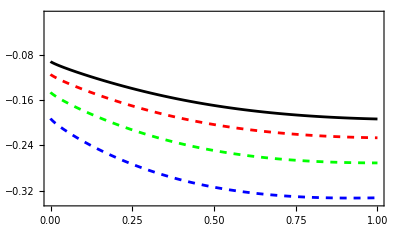

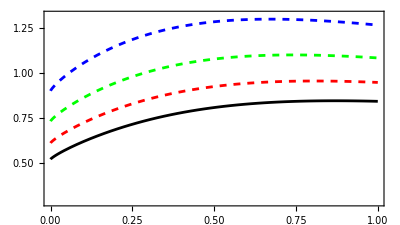

/Users/bakhodir/Theoretical Astrophysics/4thProjectQNM/freqIm2.pdf

/Users/bakhodir/Theoretical Astrophysics/4thProjectQNM/freqRe2.pdf

```mathematica
freqIm2=Plot[{ω1[0.,λ,2,0,0.2]//Im,ω1[0.1,λ,2,0,0.2]//Im,ω1[0.2,λ,2,0,0.2]//Im,ω1[0.3,λ,2,0,0.2]//Im},{λ,0,1},Frame->True,FrameLabel->{MaTeX["\lambda",Magnification->1.3],MaTeX["Im{(\omega)}",Magnification->1.3],MaTeX["\ell=2, m=0.2, n=0",Magnification->1.3]},PlotLegends->Placed[LineLegend[{MaTeX["k=0",Magnification->1.3],MaTeX["k=0.1",Magnification->1.3],MaTeX["k=0.2",Magnification->1.3],MaTeX["k=0.3",Magnification->1.3]},LegendLayout->{"Row",2}],{Scaled[{0.6,0.8}],{0.5,0.5}}],PlotStyle->{Black,{Red,Dashed},{Green,Dashed},{Blue,Dashed}},LabelStyle->{FontFamily->"Times",Black,FontSize->14},AspectRatio->9/16,PlotRange->{{0,1},{-0.34,-0.01}}]


freqRe2=Plot[{ω1[0.,λ,2,0,0.2]//Re,ω1[0.1,λ,2,0,0.2]//Re,ω1[0.2,λ,2,0,0.2]//Re,ω1[0.3,λ,2,0,0.2]//Re},{λ,0,1},Frame->True,FrameLabel->{MaTeX["\lambda",Magnification->1.3],MaTeX["Re{(\omega)}",Magnification->1.3],MaTeX["\ell=2, m=0.2, n=0",Magnification->1.3]},PlotLegends->Placed[LineLegend[{MaTeX["k=0",Magnification->1.3],MaTeX["k=0.1",Magnification->1.3],MaTeX["k=0.2",Magnification->1.3],MaTeX["k=0.3",Magnification->1.3]},LegendLayout->{"Row",2}],{Scaled[{0.65,0.2}],{0.5,0.5}}],PlotStyle->{Black,{Red,Dashed},{Green,Dashed},{Blue,Dashed}},LabelStyle->{FontFamily->"Times",Black,FontSize->14},AspectRatio->9/16,PlotRange->{{0,0.999},{0.28,1.32}}]
Export["/Users/bakhodir/Theoretical Astrophysics/4thProjectQNM/freqIm2.pdf",freqIm2,"PDF"]
Export["/Users/bakhodir/Theoretical Astrophysics/4thProjectQNM/freqRe2.pdf",freqRe2,"PDF"]
```

```mathematica
MaTeX["\\mathrm{Re}(\\omega)"]
```

-Graphics-

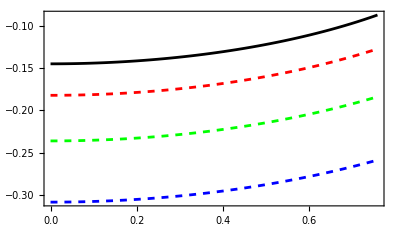

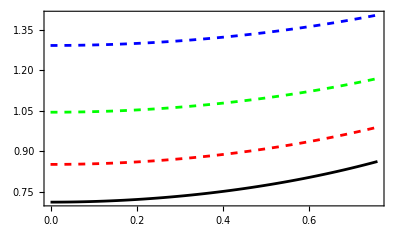

/Users/bakhodir/Theoretical Astrophysics/4thProjectQNM/mImagfreq1.pdf

/Users/bakhodir/Theoretical Astrophysics/4thProjectQNM/mRealfreq1.pdf

```mathematica
mImagfreq1=Plot[{ω1[0.1,0.1,2,0,m]//Im,ω1[0.2,0.1,2,0,m]//Im,ω1[0.3,0.1,2,0,m]//Im,ω1[0.39,0.1,2,0,m]//Im},{m,0,0.76},Frame->True,FrameLabel->{MaTeX["m",Magnification->1.3],MaTeX["Im{(\omega)}",Magnification->1.3],MaTeX["\ell=2, \lambda=0.1, n=0",Magnification->1.3]},PlotLegends->Placed[{MaTeX["k=0",Magnification->1.3],MaTeX["k=0.1",Magnification->1.3],MaTeX["k=0.2",Magnification->1.3],MaTeX["k=0.3",Magnification->1.3]},{Scaled[{0.2,0.38}],{0.5,0.5}}],PlotStyle->{Black,{Red,Dashed},{Green,Dashed},{Blue,Dashed}},LabelStyle->{FontFamily->"Times",Black,FontSize->14},AspectRatio->9/16]


mRealfreq1=Plot[{ω1[0.1,0.1,2,0,m]//Re,ω1[0.2,0.1,2,0,m]//Re,ω1[0.3,0.1,2,0,m]//Re,ω1[0.39,0.1,2,0,m]//Re},{m,0,0.76},Frame->True,FrameLabel->{MaTeX["m",Magnification->1.3],MaTeX["Re{(\omega)}",Magnification->1.3],MaTeX["\ell=2, \lambda=0.1, n=0",Magnification->1.3]},PlotLegends->Placed[{MaTeX["k=0",Magnification->1.3],MaTeX["k=0.1",Magnification->1.3],MaTeX["k=0.2",Magnification->1.3],MaTeX["k=0.3",Magnification->1.3]},{Scaled[{0.2,0.65}],{0.5,0.5}}],PlotStyle->{Black,{Red,Dashed},{Green,Dashed},{Blue,Dashed}},LabelStyle->{FontFamily->"Times",Black,FontSize->14},AspectRatio->9/16]
Export["/Users/bakhodir/Theoretical Astrophysics/4thProjectQNM/mImagfreq1.pdf",mImagfreq1,"PDF"]
Export["/Users/bakhodir/Theoretical Astrophysics/4thProjectQNM/mRealfreq1.pdf",mRealfreq1,"PDF"]
```

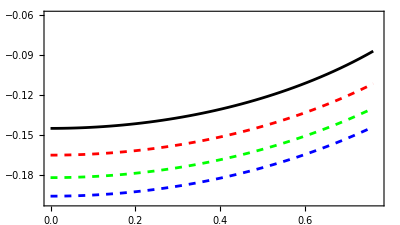

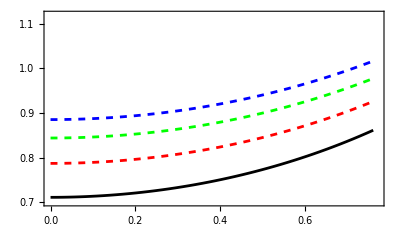

/Users/bakhodir/Theoretical Astrophysics/4thProjectQNM/mImagfreq2.pdf

/Users/bakhodir/Theoretical Astrophysics/4thProjectQNM/mrRealfreq2.pdf

```mathematica
mImagfreq2=Plot[{ω1[0.1,0.1,2,0,m]//Im,ω1[0.1,0.2,2,0,m]//Im,ω1[0.1,0.3,2,0,m]//Im,ω1[0.1,0.4,2,0,m]//Im},{m,0,0.76},Frame->True,FrameLabel->{MaTeX["m",Magnification->1.3],MaTeX["Im{(\omega)}",Magnification->1.3],MaTeX["\ell=2, k=0.1, n=0",Magnification->1.3]},(*PlotLegends->Placed[{MaTeX["\lambda=0.1",Magnification->1.3],MaTeX["\lambda=0.2",Magnification->1.3],MaTeX["\lambda=0.3",Magnification->1.3],MaTeX["\lambda=0.4",Magnification->1.3],LegendLayout->"Row",2},{Scaled[{0.15,0.7}],{0.5,0.5}}]*)PlotLegends->Placed[LineLegend[{Black,Directive[Red,Dashed],Directive[Green,Dashed],Directive[Blue,Dashed]},{MaTeX["\\lambda=0.1",Magnification->1.3],MaTeX["\\lambda=0.2",Magnification->1.3],MaTeX["\\lambda=0.3",Magnification->1.3],MaTeX["\\lambda=0.4",Magnification->1.3]},LegendLayout->{"Column",2}],{Scaled[{0.4,0.8}],{0.5,0.5}}],PlotStyle->{Black,{Red,Dashed},{Green,Dashed},{Blue,Dashed}},LabelStyle->{FontFamily->"Times",Black,FontSize->14},AspectRatio->9/16,PlotRange->{{0,0.77},{-0.2,-0.06}}]

mrRealfreq2=Plot[{ω1[0.1,0.1,2,0,m]//Re,ω1[0.1,0.2,2,0,m]//Re,ω1[0.1,0.3,2,0,m]//Re,ω1[0.1,0.4,2,0,m]//Re},{m,0,0.76},Frame->True,FrameLabel->{MaTeX["m",Magnification->1.3],MaTeX["Re{(\omega)}",Magnification->1.3],MaTeX["\ell=2, k=0.1, n=0",Magnification->1.3]},PlotLegends->Placed[LineLegend[{MaTeX["\lambda=0.1",Magnification->1.3],MaTeX["\lambda=0.2",Magnification->1.3],MaTeX["\lambda=0.3",Magnification->1.3],MaTeX["\lambda=0.4",Magnification->1.3]},LegendLayout->{"Row",2}],{Scaled[{0.4,0.8}],{0.5,0.5}}],PlotStyle->{Black,{Red,Dashed},{Green,Dashed},{Blue,Dashed}},LabelStyle->{FontFamily->"Times",Black,FontSize->14},AspectRatio->9/16,PlotRange->{{0,0.77},{0.7,1.12}}]
Export["/Users/bakhodir/Theoretical Astrophysics/4thProjectQNM/mImagfreq2.pdf",mImagfreq2,"PDF"]
Export["/Users/bakhodir/Theoretical Astrophysics/4thProjectQNM/mrRealfreq2.pdf",mrRealfreq2,"PDF"]
```

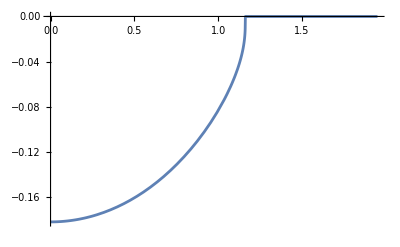

```mathematica
Plot[ω1[0.1,0.3,2,0,m]//Im,{m,0,1.95}]
```

### other.

```mathematica
Clear[U,V3,V4,ω12,V]
```

```mathematica
Solve[I((ω^2-V)/(√(-2 U)))+ 1/(2 U)(1/8 V4/U (1/4 + (n+1/2)^2)-1/288 (V3/U)^2(7+60 (n+1/2)^2))== n+1/2,ω]
```

{{ω→-((-2)^(1/4) √U √(1/2+n-(ⅈ √-U V)/(√2 U)+(11 V3^2)/(288 U^3)+(5 n V3^2)/(48 U^3)+(5 n^2 V3^2)/(48 U^3)-V4/(32 U^2)-(n V4)/(16 U^2)-(n^2 V4)/(16 U^2)))/(-U)^(1/4)},{ω→((-2)^(1/4) √U √(1/2+n-(ⅈ √-U V)/(√2 U)+(11 V3^2)/(288 U^3)+(5 n V3^2)/(48 U^3)+(5 n^2 V3^2)/(48 U^3)-V4/(32 U^2)-(n V4)/(16 U^2)-(n^2 V4)/(16 U^2)))/(-U)^(1/4)}}

```mathematica
U:=f[rp[k,λ,l,m],k,λ]^2 (Vp[k,λ,l,m])
V:=Veff[rp[k,λ,l,m],l,k,λ,m]
V3:=2 f[r,k,λ]^2 D[f[r,k,λ],r] D[Veff[r,l,k,λ,m],{r,2}] + f[r,k,λ]^3 D[Veff[r,l,k,λ,m],{r,3}]/.r->rp[k,λ,l,m]
V4:=4 f[r,k,λ]^2 (D[f[r,k,λ],r])^2 Vp[k,λ,l,m] + 2 f[r,k,λ]^3 D[f[r,k,λ],{r,2}] Vp[k,λ,l,m]+2 f[r,k,λ]^5 D[f[r,k,λ],r] Vp3[k,λ,l,m] + 3 f[r,k,λ]^3 D[f[r,k,λ],r] Vp3[k,λ,l,m] + f[r,k,λ]^4 Vp4[k,λ,l,m]/.r->rp[k,λ,l,m]
```

```mathematica
ω12[k_,λ_,l_,m_,n_]:=-((-2)^(1/4) √U √(1/2+n-(ⅈ √-U V)/(√2 U)+(11 V3^2)/(288 U^3)+(5 n V3^2)/(48 U^3)+(5 n^2 V3^2)/(48 U^3)-V4/(32 U^2)-(n V4)/(16 U^2)-(n^2 V4)/(16 U^2)))/(-U)^(1/4)
```

```mathematica
ω12[0.6,0.5,2,0.1,3]
```

-(((-2)^(1/4) √(f[rp[k,λ,l,m],k,λ]^2 Vp[k,λ,l,m]) √(7/2-(ⅈ Veff[rp[k,λ,l,m],l,k,λ,m] √(-f[rp[k,λ,l,m],k,λ]^2 Vp[k,λ,l,m]))/(√2 f[rp[k,λ,l,m],k,λ]^2 Vp[k,λ,l,m])+(371 (2 f[rp[k,λ,l,m],k,λ]^2 f^(1,0,0)[rp[k,λ,l,m],k,λ] Veff^(2,0,0,0,0)[rp[k,λ,l,m],l,k,λ,m]+f[rp[k,λ,l,m],k,λ]^3 Veff^(3,0,0,0,0)[rp[k,λ,l,m],l,k,λ,m])^2)/(288 f[rp[k,λ,l,m],k,λ]^6 Vp[k,λ,l,m]^3)-(25 (4 f[rp[k,λ,l,m],k,λ]^2 Vp[k,λ,l,m] (f^(1,0,0)[rp[k,λ,l,m],k,λ])^2+2 f[rp[k,λ,l,m],k,λ]^3 Vp[k,λ,l,m] f^(2,0,0)[rp[k,λ,l,m],k,λ]+3 f[rp[k,λ,l,m],k,λ]^3 f^(1,0,0)[rp[k,λ,l,m],k,λ] Veff^(3,0,0,0,0)[rp[k,λ,l,m],l,k,λ,m]+2 f[rp[k,λ,l,m],k,λ]^5 f^(1,0,0)[rp[k,λ,l,m],k,λ] Veff^(3,0,0,0,0)[rp[k,λ,l,m],l,k,λ,m]+f[rp[k,λ,l,m],k,λ]^4 Veff^(4,0,0,0,0)[rp[k,λ,l,m],l,k,λ,m]))/(32 f[rp[k,λ,l,m],k,λ]^4 Vp[k,λ,l,m]^2)))/(-f[rp[k,λ,l,m],k,λ]^2 Vp[k,λ,l,m])^(1/4))

```mathematica
V4[]
```

(4 f[rp[k,λ,l,m],k,λ]^2 Vp[k,λ,l,m] (f^(1,0,0)[rp[k,λ,l,m],k,λ])^2+2 f[rp[k,λ,l,m],k,λ]^3 Vp[k,λ,l,m] f^(2,0,0)[rp[k,λ,l,m],k,λ]+3 f[rp[k,λ,l,m],k,λ]^3 f^(1,0,0)[rp[k,λ,l,m],k,λ] Veff^(3,0,0,0,0)[rp[k,λ,l,m],l,k,λ,m]+2 f[rp[k,λ,l,m],k,λ]^5 f^(1,0,0)[rp[k,λ,l,m],k,λ] Veff^(3,0,0,0,0)[rp[k,λ,l,m],l,k,λ,m]+f[rp[k,λ,l,m],k,λ]^4 Veff^(4,0,0,0,0)[rp[k,λ,l,m],l,k,λ,m])[]

## data

```mathematica
data=Import["/Users/bakhodir/Theoretical Astrophysics/4thProjectQNM/wave_data.txt","Table"];
dataQNM=Select[data,40<#[[1]]<330&];
```

```mathematica
dataQNM={#[[1]],#[[2]]/Max[Abs[dataQNM[[All,2]]]]}&/@dataQNM;
```

```mathematica
fit=NonlinearModelFit[dataQNM,A Exp[-wi t] Cos[wr t],{{A,1},{wi,0.15},{wr,0.7}},t,MaxIterations->5000];
```

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

FittedModels`FindNonlinearModelFit::vloc: The variable TerminatedEvaluation[RecursionLimit][wi] cannot be localized so that it can be assigned to numerical values.

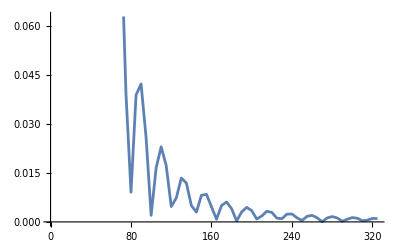

```mathematica
ListLinePlot[dataQNM]
```

```mathematica
params=fit["BestFitParameters"];

wr=params["wr"];
wi=params["wi"];

omega=wr-I*wi
```

FittedModels`FindNonlinearModelFit::vloc: The variable TerminatedEvaluation[RecursionLimit][wi] cannot be localized so that it can be assigned to numerical values.

General::stop: Further output of FittedModels`FindNonlinearModelFit::vloc will be suppressed during this calculation.

-ⅈ NonlinearModelFit[{{40.,1.},{45.,0.819976},{50.,0.0755176},{55.,0.102283},{60.,0.0742907},{65.,0.098432},{70.,0.0888581},{75.,0.0392015},{80.,0.0091077},{85.,0.0388363},{90.,0.0422555},{95.,0.025777},{100.,0.00199988},{105.,0.0166049},{110.,0.0230095},{115.,0.0172322},{120.,0.00469942},{125.,0.00734239},{130.,0.0134209},{135.,0.0119155},{140.,0.00501801},{145.,0.00300045},{150.,0.00813593},{155.,0.00845329},{160.,0.00462502},{165.,0.00082409},{170.,0.00500813},{175.,0.00610181},{180.,0.00404346},{185.,0.000299514},{190.,0.00306128},{195.,0.00444819},{200.,0.00344979},{205.,0.000873774},{210.,0.00180591},{215.,0.00325267},{220.,0.00290278},{225.,0.00114665},{230.,0.000977293},{235.,0.00236951},{240.,0.00241858},{245.,0.00124858},{250.,0.0004233},{255.,0.0017064},{260.,0.0019976},{265.,0.00125184},{270.,0.0000520426},{275.,0.00120268},{280.,0.00163476},{285.,0.00119819},{290.,0.000194338},{295.,0.00081719},{300.,0.0013235},{305.,0.00111254},{310.,0.000353589},{315.,0.000521153},{320.,0.00105734},{325.,0.00101016}},A ⅇ^(-t TerminatedEvaluation[RecursionLimit][wi]) Cos[t TerminatedEvaluation[RecursionLimit]],{{A,1},{TerminatedEvaluation[RecursionLimit][wi],0.15},{TerminatedEvaluation[RecursionLimit],0.7}},t,MaxIterations→5000][BestFitParameters][wi]+NonlinearModelFit[{{40.,1.},{45.,0.819976},{50.,0.0755176},{55.,0.102283},{60.,0.0742907},{65.,0.098432},{70.,0.0888581},{75.,0.0392015},{80.,0.0091077},{85.,0.0388363},{90.,0.0422555},{95.,0.025777},{100.,0.00199988},{105.,0.0166049},{110.,0.0230095},{115.,0.0172322},{120.,0.00469942},{125.,0.00734239},{130.,0.0134209},{135.,0.0119155},{140.,0.00501801},{145.,0.00300045},{150.,0.00813593},{155.,0.00845329},{160.,0.00462502},{165.,0.00082409},{170.,0.00500813},{175.,0.00610181},{180.,0.00404346},{185.,0.000299514},{190.,0.00306128},{195.,0.00444819},{200.,0.00344979},{205.,0.000873774},{210.,0.00180591},{215.,0.00325267},{220.,0.00290278},{225.,0.00114665},{230.,0.000977293},{235.,0.00236951},{240.,0.00241858},{245.,0.00124858},{250.,0.0004233},{255.,0.0017064},{260.,0.0019976},{265.,0.00125184},{270.,0.0000520426},{275.,0.00120268},{280.,0.00163476},{285.,0.00119819},{290.,0.000194338},{295.,0.00081719},{300.,0.0013235},{305.,0.00111254},{310.,0.000353589},{315.,0.000521153},{320.,0.00105734},{325.,0.00101016}},A ⅇ^(-t TerminatedEvaluation[RecursionLimit][wi]) Cos[t TerminatedEvaluation[RecursionLimit]],{{A,1},{TerminatedEvaluation[RecursionLimit][wi],0.15},{TerminatedEvaluation[RecursionLimit],0.7}},t,MaxIterations→5000][BestFitParameters][wr]

```mathematica
ClearAll["Global`*"]
```

```mathematica
data={{40.,1.},{45.,0.819976},{50.,0.0755176},{55.,0.102283},{60.,0.0742907},{65.,0.098432},{70.,0.0888581},{75.,0.0392015},{80.,0.0091077},{85.,0.0388363},{90.,0.0422555},{95.,0.025777},{100.,0.00199988},{105.,0.0166049},{110.,0.0230095},{115.,0.0172322},{120.,0.00469942},{125.,0.00734239},{130.,0.0134209}};
```

```mathematica
data={#[[1]],#[[2]]/Max[Abs[data[[All,2]]]]} & /@ data;
```

```mathematica
fit=NonlinearModelFit[data,A Exp[-wi t] Cos[wr t],{{A,1},{wi,0.021},{wr,0.8}},t,MaxIterations->5000];
```

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 5000 iterations.

```mathematica
params=fit["BestFitParameters"]
```

{A→4.82186×10^42,wi→2.18435,wr→0.824668}

```mathematica
wr=params["wr"];
wi=params["wi"];
omega = wr - I wi;
```

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

## greyBody factor calculations

```mathematica
k=0.1;
λ=0.1;
m=0.1;
```

```mathematica
V0 := Veff[r,l,k,λ,m]/.r->rp[k,λ,l,m]
V2 := f[r,k,λ] D[f[r,k,λ],r] D[Veff[r,l,k,λ,m],r] + (f[r,k,λ])^2 D[Veff[r,l,k,λ,m],r,r]/.r->rp[k,λ,l,m]
```

```mathematica
Γ[ω_]:= (1 + Exp[(2 Pi (V0 - ω^2))/(√(-2 V2))])
```

```mathematica
Γ[0.01]//N
```

FindRoot::nlnum: The function value {0.0347222 (4.90108+4.2 l+4.2 l^2-0.1 (17.378+12.2 l+12.2 l^2)-0.299573 (16.68+6. (-1.+l+Power[«2»])-0.1 (16.68+Times[«2»]+Times[«2»])))} is not a list of numbers with dimensions {1} at {r} = {2.}.

ReplaceAll::reps: {FindRoot[-(16-6 r+6 l r+6 l^2 r-2 l Power[«2»]-2 Power[«2»] Power[«2»]+2 0.1^2 r^3+12 0.1-4 r 0.1+l r 0.1+«6»)/Times[«2»]==0,{r,2}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {0.0347222 (4.90108+4.2 l+4.2 l^2-0.1 (17.378+12.2 l+12.2 l^2)-0.299573 (16.68+6. (-1.+l+Power[«2»])-0.1 (16.68+Times[«2»]+Times[«2»])))} is not a list of numbers with dimensions {1} at {r} = {2.}.

ReplaceAll::reps: {FindRoot[-(16-6 r+6 l r+6 l^2 r-2 l Power[«2»]-2 Power[«2»] Power[«2»]+2 0.1^2 r^3+12 0.1-4 r 0.1+l r 0.1+«6»)/Times[«2»]==0,{r,2}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {0.0347222 (4.90108+4.2 l+4.2 l^2-0.1 (17.378+12.2 l+12.2 l^2)-0.299573 (16.68+6. (-1.+l+Power[«2»])-0.1 (16.68+Times[«2»]+Times[«2»])))} is not a list of numbers with dimensions {1} at {r} = {2.}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[-(16-6 r+6 l r+6 l^2 r-2 l Power[«2»]-2 Power[«2»] Power[«2»]+2 0.1^2 r^3+12 0.1-4 r 0.1+l r 0.1+«6»)/Times[«2»]==0,{r,2}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

```mathematica
Plot[Γ[x],{x,0,1}]
```

FindRoot::nlnum: The function value {0.0347222 (4.90108+4.2 l+4.2 l^2-0.1 (17.378+12.2 l+12.2 l^2)-0.299573 (16.68+6. (-1.+l+Power[«2»])-0.1 (16.68+Times[«2»]+Times[«2»])))} is not a list of numbers with dimensions {1} at {r} = {2.}.

ReplaceAll::reps: {FindRoot[-(16-6 r+6 l r+6 l^2 r-2 l Power[«2»]-2 Power[«2»] Power[«2»]+2 0.1^2 r^3+12 0.1-4 r 0.1+l r 0.1+«6»)/Times[«2»]==0,{r,2}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {0.0347222 (4.90108+4.2 l+4.2 l^2-0.1 (17.378+12.2 l+12.2 l^2)-0.299573 (16.68+6. (-1.+l+Power[«2»])-0.1 (16.68+Times[«2»]+Times[«2»])))} is not a list of numbers with dimensions {1} at {r} = {2.}.

ReplaceAll::reps: {FindRoot[-(16-6 r+6 l r+6 l^2 r-2 l Power[«2»]-2 Power[«2»] Power[«2»]+2 0.1^2 r^3+12 0.1-4 r 0.1+l r 0.1+«6»)/Times[«2»]==0,{r,2}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {0.0347222 (4.90108+4.2 l+4.2 l^2-0.1 (17.378+12.2 l+12.2 l^2)-0.299573 (16.68+6. (-1.+l+Power[«2»])-0.1 (16.68+Times[«2»]+Times[«2»])))} is not a list of numbers with dimensions {1} at {r} = {2.}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[-(16-6 r+6 l r+6 l^2 r-2 l Power[«2»]-2 Power[«2»] Power[«2»]+2 0.1^2 r^3+12 0.1-4 r 0.1+l r 0.1+«6»)/Times[«2»]==0,{r,2}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

$Aborted

```mathematica
Vp3[k_,λ_,l_,m_]:=D[Veff[r,l,k,λ,m],{r,3}]/.r->rp[k,λ,l,m]
V
```